# VYA - Přednášky

## 9. Přednáška

### Funkce Ser a Par pro RLC

```mathematica
Quiet[Remove["Global`*"]];
```

U_R = R * I_R     => Z_R = R
U_L = jωL * I_L     => Z_L = jωL
U_C = 1/JωC* I_C     => Z_C = 1/jωC

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Ser[{R1,R2,R3,R4}]
```

R1+R2+R3+R4

```mathematica
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Par[{R1,R2,R3,R4}]
```

1/(1/R1+1/R2+1/R3+1/R4)

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
Uz = 10*Sin[cos[t] + 0.123]
Um = 10.;
fi = 0.123;
ω = 1000;
T = (2Pi)/ω;
UzFaz = Um * E^(I*ω)
```

10 Sin[0.123+cos[t]]

5.62379+8.2688 ⅈ

```mathematica
Rovn = {
Iuz == IR1 + IC,
IR1 + IC == IR2 + IL,

U1 == R2 * IR2,
U1 ==  I * ω * L * IL,
UzFaz - U1 == R1 * IR1,
UzFaz - U1 == 1/(I * ω * Cl)* IC
}
```

{Iuz==IC+IR1,IC+IR1==IL+IR2,U1==200 IR2,U1==33 ⅈ IL,(5.62379+8.2688 ⅈ)-U1==100 IR1,(5.62379+8.2688 ⅈ)-U1==(0.-212.766 ⅈ) IC}

```mathematica
Neznam =Union[Cases[Rovn, _Symbol, {0, ∞}]];
Length /@ {Rovn, Neznam};
Res = Solve[Rovn][[1]];
```

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Z1 = Par[{R1, 1/(I * ω * Cl)}]
Z2 = Par[{R2, I * ω * L}]
```

1/(1/R1+ⅈ Cl ω)

1/(1/R2-ⅈ/(L ω))

```mathematica
IUZDel = UzFaz/Ser[{Z1, Z2}]
Iuz /. Res
```

UzFaz/Ser[{1/(1/R1+ⅈ Cl ω),1/(1/R2-ⅈ/(L ω))}]

ReplaceAll::reps: {Res} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Iuz/.Res

```mathematica
U1Del = UzFaz * Z2/(Z1 + Z2)  //Simplify
U1Del /. ω -> 0
Limit[U1Del, ω -> ∞]
```

(L R2 UzFaz ω (-ⅈ+Cl R1 ω))/(-ⅈ L R1 ω-ⅈ L R2 ω+R1 R2 (-1+Cl L ω^2))

0

UzFaz

```mathematica
?Chop
```

### Přenosná funkce

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
Uz = 10*Sin[cos[t] + 0.123]
Um = 10.;
fi = 0.123;
ω = 1000;
T = (2Pi)/ω;
UzFaz = Um * E^(I*ω)
```

10 Sin[0.123+cos[t]]

5.62379+8.2688 ⅈ

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Z1 = Par[{R1, 1/(I * ω * Cl)}]
Z2 = Par[{R2, I * ω * L}]
```

1/(1/R1+ⅈ Cl ω)

1/(1/R2-ⅈ/(L ω))

```mathematica
IUZDel = UzFaz/Ser[{Z1, Z2}]
U1Del = UzFaz * Z2/(Z1 + Z2)  //Simplify
```

UzFaz/(1/(1/R2-ⅈ/(L ω))+1/(1/R1+ⅈ Cl ω))

(L R2 UzFaz ω (-ⅈ+Cl R1 ω))/(-ⅈ L R1 ω-ⅈ L R2 ω+R1 R2 (-1+Cl L ω^2))

```mathematica
Prenos = U1Del/UzFaz //Simplify
```

(L R2 ω (-ⅈ+Cl R1 ω))/(-ⅈ L R1 ω-ⅈ L R2 ω+R1 R2 (-1+Cl L ω^2))

```mathematica
L= 33 mH;
mH = 10^-3;
Cl = 4.7 υF;
υF = 10^-6;
R1 = 100;
R2 = 200;
```

```mathematica
Prenos = U1Del/UzFaz //Simplify
```

(1. ω ((0.-2127.66 ⅈ)+1. ω))/(-6.44745×10^6-(0.+3191.49 ⅈ) ω+1. ω^2)

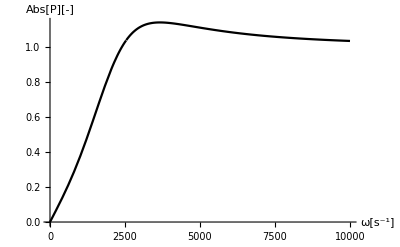

```mathematica
Plot[Abs[Prenos], {ω, 0.1, 10^4}, PlotStyle->Black, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

### Řešení obvodu

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Ser[OdporSer_]:=Total[OdporSer]
Par[OdporPar_]:=Total[OdporPar^-1]^-1
Z1 = Ser[{R1, I * ω * L1, 1/(I * ω * C1)}];
Z2 = Par[{Ser[{R2, I * ω * L2}], 1/(I * ω * C2)}];
Prenos = Z2/(Z1 + Z1);
```

```mathematica
R1 = 1;
R2 = 1;
L1 = 10^-3;
L2 = 10^-6;
C1 = 10^-6;
C2 = 10^-9;
```

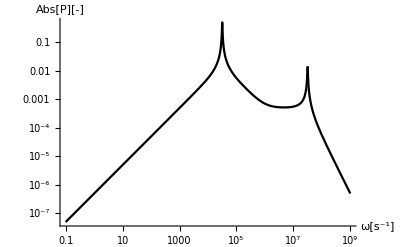

```mathematica
LogLogPlot[Abs[Prenos], {ω, 0.1, 10^9}, PlotStyle->Black, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

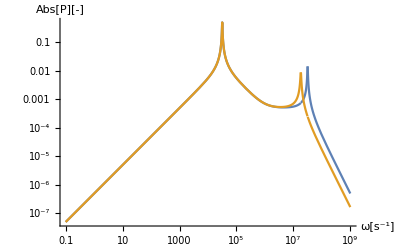

```mathematica
Clear[C2];
LogLogPlot[Evaluate[Abs[Prenos] /. {{C2 -> 10^-9}, {C2 -> 3*10^-9}}], {ω, 0.1, 10^9}, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

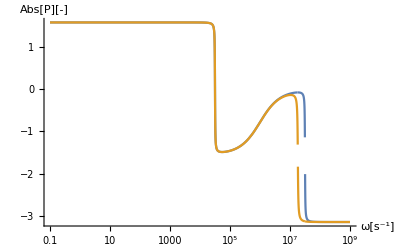

```mathematica
LogLinearPlot[Evaluate[Arg[Prenos] /. {{C2 -> 10^-9}, {C2 -> 3*10^-9}}], {ω, 0.1, 10^9}, AxesLabel->{"ω[s^-1]", "Abs[P][-]"}, GridLines->Full, PlotRange->All]
```

### Hledání funkcí

```mathematica
?*Plot*
```